Todo: 100 random coins

```mathematica
try[num_,time_]:=Block[{start=0,list},list=PadRight[SparseArray[Rule@@@Tally@#],num]&/@RandomInteger[{1,num},{time,num}];
FoldList[#1-1+#2&,ConstantArray[start,num],list]]
data=try[32,10000];(*无破产模型*)draw=BarChart[#,ChartStyle->24,BarSpacing->{0,0},Axes->None,PerformanceGoal->"Speed"]&;
pic=(draw[#-Min[#]])&/@Part[data,Range[1,10000,50]];
picS=(draw@Sort[#-Min[#]]&)/@Part[data,Range[1,10000,50]];
```

```mathematica
CDF[OrderDistribution[{NormalDistribution[μ,σ],1},1],x]
CDF[NormalDistribution[μ,σ],x]
```

1/2 Erfc[(-x+μ)/(√2 σ)]

1/2 Erfc[(-x+μ)/(√2 σ)]

```mathematica
D[(1/2 Erfc[(-x+μ)/(√2 σ)]), x]
```

(ⅇ^(-(-x+μ)^2/(2 σ^2)))/(√(2 π) σ)

```mathematica
Quantile[NormalDistribution[μ,σ],q/"N"]
```

ConditionalExpression[μ-√2 σ InverseErfc[(2 q)/N],0≤q/N≤1]

```mathematica
NormalDistribution[μ,σ]
```

NormalDistribution[μ,σ]

```mathematica
CDF[WeibullDistribution[α,β,μ],x]
```

Piecewise[{{1-ⅇ^(-((x-μ)/β)^α), x>μ}, {0, True}}]

{5.9697,Null}

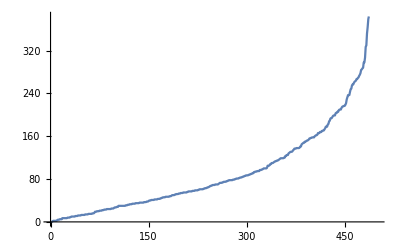

```mathematica
num=500;time=10000;start=100;
cf=With[{num=num,start=start},
Compile[{{times,_Integer}},
Module[{moneylist,index},
moneylist=ConstantArray[start,num];index=Range[num];
Do[Scan[moneylist[[#]]++&,MapThread[If[#1≥k,#2+UnitStep[#2-#3],#3]&,{moneylist,RandomInteger[{1,num-1},num],index}]],{k,times}];
moneylist-times]]];
ans2=cf[10^5];//AbsoluteTiming
ListLinePlot@Sort@ans2
```

```mathematica
WeibullDistribution[1,100,-0.09435533733411265]
```

WeibullDistribution[1,100,-0.0943553]

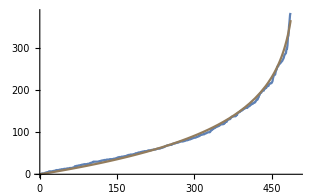

```mathematica
Plot[-100 Log[1-x/500],{x,0,500},ColorFunction->"DarkRainbow"];
ListLinePlot[Sort@ans2];
Show[%,%%]
```

```mathematica
Quantile[WeibullDistribution[α,β,μ],q/"N"]
Quantile[ExponentialDistribution[λ],q/"N"]
Mean@WeibullDistribution[α,β,μ]
Mean@ExponentialDistribution[λ]
```

ConditionalExpression[Piecewise[{{μ+β (-Log[1-q/N])^(1/α), 0<q/N<1}, {μ, q/N≤0}, {∞, True}}],0≤q/N≤1]

ConditionalExpression[Piecewise[{{-Log[1-q/N]/λ, q/N<1}, {∞, True}}],0≤q/N≤1]

μ+β Gamma[1+1/α]

1/λ

```mathematica
FindDistribution[ans,3,"CramerVonMises"]//TableForm
```

NormalDistribution[100.012,107.368] | 0.995242
StudentTDistribution[104.803,105.707,19.7554] | 0.537763
LogisticDistribution[104.759,63.2838] | 0.467419

```mathematica
FindDistribution[ans2,3,"CramerVonMises"]//TableForm
```

WeibullDistribution[1.0553,97.609,-0.466025] | 0.452366
ParetoDistribution[899.179,11.0584,0.960746,-0.444266] | 0.0606171
FrechetDistribution[2.2034,97.3579,-52.2122] | 0.0140688

Piecewise[{{ⅇ^(-t/100)/100, t>0}, {0, True}}]

Piecewise[{{ⅇ^(-t/100)/100, t≥0}, {0, True}}]

ConditionalExpression[Piecewise[{{-100 Log[1-t], t<1}, {∞, True}}],0≤t≤1]

x-(-1+x) Log[1-x]

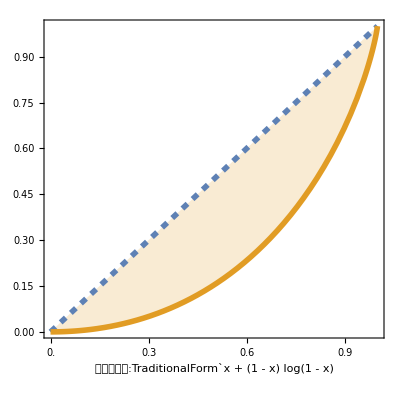

```mathematica
PDF[WeibullDistribution[1,100,0],t]
PDF[ExponentialDistribution[1/100],t]
InverseCDF[ExponentialDistribution[1/100],t]
Integrate[-100 Log[1-t],{t,0,x},Assumptions->0<x<1]/Integrate[-100 Log[1-t],{t,0,1}]
img=Plot[{Style[x,Dashed,Thickness[0.01]],Style[x-(-1+x) Log[1-x],Thickness[0.01]]},{x,0,1},Filling->{2->{1}},PlotRange->{0,1},AspectRatio->1,Axes->False,Frame->True,FrameTicks->{Table[i,{i,0,1,0.1}],Automatic},FrameLabel->{"劳伦兹曲线:\!\(\*TagBox[\(TraditionalForm\`x + \((1 - x)\)\\\ \(log(1 - x)\)\),
TraditionalForm,\nEditable->True]\)",None,"基尼系数=0.5"},BaseStyle->FontSize->12]
```